```mathematica
T1 = {1.45,1.63,1.59,1.63,1.62,1.63,1.55,1.66,1.57,1.57,1.51,1.63,1.49,1.54,1.66,1.59,1.63,1.60,1.69,1.52,1.67,1.59,1.66,1.59,1.56,1.56,1.60,1.59,1.57,1.58}
Length[T1]
```

{1.45,1.63,1.59,1.63,1.62,1.63,1.55,1.66,1.57,1.57,1.51,1.63,1.49,1.54,1.66,1.59,1.63,1.6,1.69,1.52,1.67,1.59,1.66,1.59,1.56,1.56,1.6,1.59,1.57,1.58}

```mathematica
30
```

```mathematica
Total[T1]
```

47.73

```mathematica
ot1 = Total[T1]/Length[T1]
```

1.591

```mathematica
StandardDeviation[T1]
```

0.0551706

```mathematica
T2 = 47.81/30
```

1.59367

```mathematica
0.3/Sqrt[30]
```

0.0547723

```mathematica
d1 = {20.6,20.8,21.8,22.9,24.9}
d3 = {60.3,63.0,63.2,68.9,72.0}
a = {0,15,30,45,60}
```

{20.6,20.8,21.8,22.9,24.9}

{60.3,63.,63.2,68.9,72.}

{0,15,30,45,60}

```mathematica
l1 = d1/10
```

{2.06,2.08,2.18,2.29,2.49}

```mathematica
{1.8100000000000003,2.06,2.08,2.18,2.29,2.49}
```

{1.81,2.06,2.08,2.18,2.29,2.49}

```mathematica
l3 = d3/30
```

{2.01,2.1,2.10667,2.29667,2.4}

```mathematica
l2 = l1+l3
```

{4.07,4.18,4.28667,4.58667,4.89}

```mathematica
l0 = l2/2
```

{2.035,2.09,2.14333,2.29333,2.445}

```mathematica
StandardDeviation[{l1,l3}]
```

{0.0353553,0.0141421,0.0518545,0.00471405,0.0636396}

```mathematica
g1={{a[[1]],l1[[1]]},{a[[2]],l1[[2]]},{a[[3]],l1[[3]]},{a[[4]],l1[[4]]},{a[[5]],l1[[5]]}}
g2={{a[[1]],l3[[1]]},{a[[2]],l3[[2]]},{a[[3]],l3[[3]]},{a[[4]],l3[[4]]},{a[[5]],l3[[5]]}}
```

{{0,1.81},{15,2.06},{30,2.08},{45,2.18},{60,2.29}}

{{0,2.01},{15,2.1},{30,2.10667},{45,2.29667},{60,2.4}}

```mathematica
line1=Fit[g1,{1,x},x]
line2=Fit[g2,{1,x},x]
```

1.868+0.0072 x

1.98733+0.00651111 x

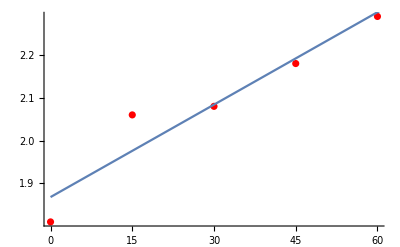

```mathematica
Show[ListPlot[g1,PlotStyle->Red],Plot[{line1},{x,0,100}]]
```

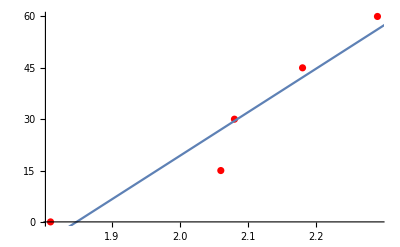

-Graphics-

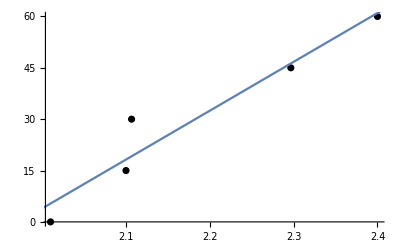

```mathematica
Show[ListPlot[g2,PlotStyle->Black],Plot[{line2},{x,0,100}]]
```

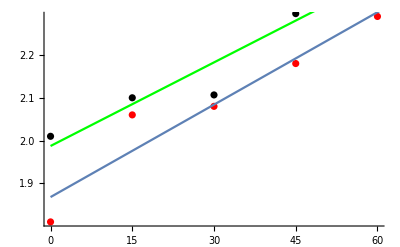

```mathematica
Show[ListPlot[g1,PlotStyle->Red],Plot[{line1},{x,0,100}],
ListPlot[g2,PlotStyle->Black],Plot[{line2},{x,0,100},PlotStyle->Green]]
```

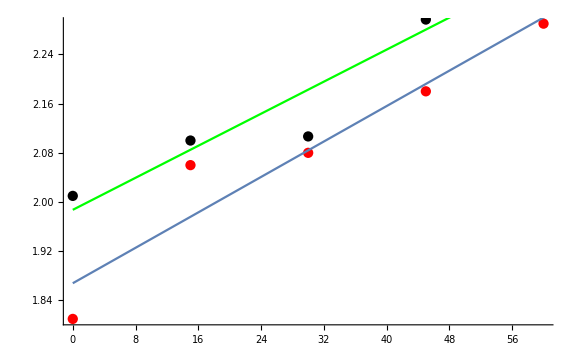

```mathematica
Show[%96,ImageSize->Large]
```

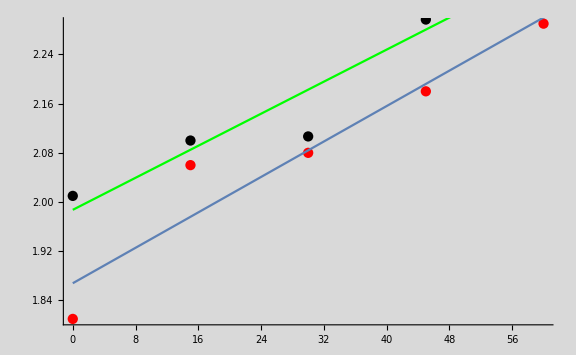

```mathematica
Show[%97,Background->LightGray]
```

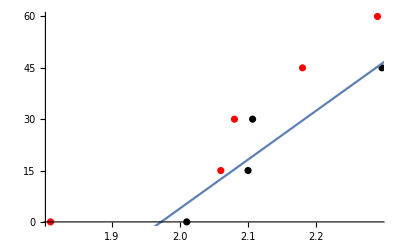

-Graphics-

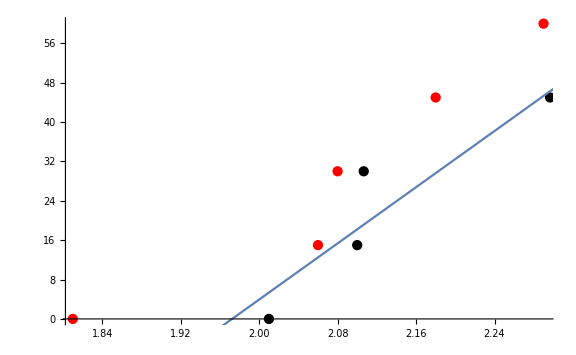

```mathematica
Show[%73,ImageSize->Large]
```

```mathematica
p1 = {1.81,1.82}
p2 = {2.06,2.01}
p3 = {2.08,2.1}
p4 = {2.18,2.10667}
p5  = {2.29,2.29667}
p6 = {2.49,2.4}
```

```mathematica
2*Pi*Sqrt{((1/4)*5
```

```mathematica
With[{a=Interval[1.01+.18 {-1,1}],b=Interval[.92+.11 {-1,1}],c=Interval[2.2+.2 {-1,1}]},Plot[{Min[a+b*x+c*x^2],1.01+.92 x+2.2 x^2,Max[a+b*x+c*x^2]},{x,-5,5},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]]
```

```mathematica
((18.1/10)+(54.6/30))/2
```

1.815

```mathematica
StandardDeviation[{18.1/10,54.6/30}]
```

0.00707107

```mathematica
gold = {{0,2.035},{15,2.09},{30,2.143},{45,2.293},{60,2.445}}
```

{{0,2.035},{15,2.09},{30,2.143},{45,2.293},{60,2.445}}

```mathematica
lineg=Fit[gold,{1,x},x]
```

1.9966+0.00682 x

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Show[ListPlot[gold,PlotStyle->Red],Plot[{lineg},{x,0,100}],
ErrorListPlot[{{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}],PlotMarkers->{"×"}],AxesLabel->{HoldForm[Abstand vom Mittelpunkt in mm],HoldForm[Periodendauer in s]},PlotLabel->HoldForm[Schwingperioden des Drehpendels],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[Show[ListPlot[gold,PlotStyle->Red],Plot[{lineg},{x,0,100}],
ErrorListPlot[{{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}],PlotMarkers->{"×"}],AxesLabel->{HoldForm[Abstand vom Mittelpunkt in mm],HoldForm[Periodendauer in s]},PlotLabel->HoldForm[Schwingperioden des Drehpendels],LabelStyle->{GrayLevel[0]}],Background->White]
```

```mathematica
Show[Show[ListPlot[gold,PlotStyle->Red],Plot[{lineg},{x,0,100}],
ErrorListPlot[{{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}],PlotMarkers->{"×"}],AxesLabel->{HoldForm[Abstand vom Mittelpunkt in mm],HoldForm[Periodendauer in s]},PlotLabel->HoldForm[Schwingperioden des Drehpendels],LabelStyle->{GrayLevel[0]}],AxesLabel->{HoldForm[Abstand vom Mittelpunkt in mm],HoldForm[Periodendauer in s]},PlotLabel->HoldForm[Schwingperioden des Drehpendels],LabelStyle->{GrayLevel[0]},Background->White]
```

```mathematica
Show[Show[ListPlot[gold,PlotStyle->Red],Plot[{lineg},{x,0,100}],
ErrorListPlot[{{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}],PlotMarkers->{"×"}],AxesLabel->{HoldForm[Abstand vom Mittelpunkt in mm],HoldForm[Periodendauer in s]},PlotLabel->HoldForm[Schwingperioden des Drehpendels],LabelStyle->{GrayLevel[0]}],ImageSize->Large,AxesLabel->{HoldForm[Abstand vom Mittelpunkt in mm],HoldForm[Periodendauer in s]},PlotLabel->HoldForm[Schwingperioden des Drehpendels],LabelStyle->{GrayLevel[0]},Background->White]
```

```mathematica
Show[ErrorListPlot[{{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}]]
```

Show::gtype: ErrorListPlot is not a type of graphics.

Show[ErrorListPlot[{{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}]]

```mathematica
data = {{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}
```

{{{0,2.035},ErrorBar[0.04]},{{15,2.09},ErrorBar[0.01]},{{30,2.143},ErrorBar[0.05]},{{45,2.293},ErrorBar[0.01]},{{60,2.445},ErrorBar[0.06]}}

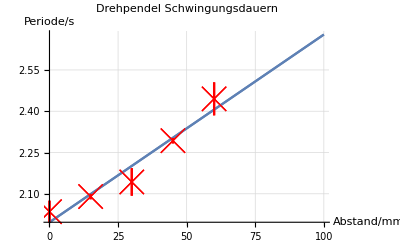

```mathematica
Show[Plot[{lineg},{x,0,100}],
ErrorListPlot[data,PlotStyle->Red,PlotMarkers->{{Graphics@{Opacity[0],Darker@Blue,Disk[]},0.01 5}}],ListPlot[gold,PlotStyle->Red,PlotMarkers->{"×",25}],%203,AxesLabel->{HoldForm[Abstand/mm],HoldForm[Periode/s]},PlotLabel->HoldForm[Drehpendel Schwingungsdauern],LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]},GridLines->Automatic]
```

```mathematica
Show[%209,Background->White]
```

-Graphics-

```mathematica
Show[%210,ImageSize->Full]
```

-Graphics-

```mathematica
Show[%211,AxesStyle->Black]
```

-Graphics-

```mathematica
Export["/Users/Andrez/Documents/gitpups/Praktikum A1/5_17/trick17.png",%212,"PNG"]
```

/Users/Andrez/Documents/gitpups/Praktikum A1/5_17/trick17.png

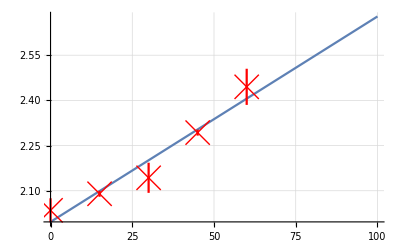

```mathematica
Show[%205,Background->White]
```

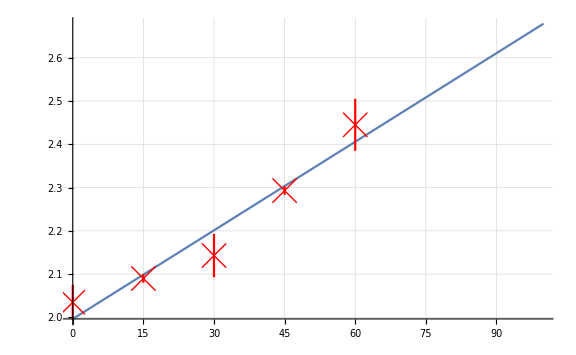

```mathematica
Show[%207,ImageSize->Large]
```

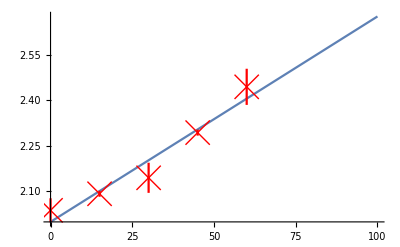

```mathematica
Show[%200,ImageSize->Full]
```

```mathematica
Show[%201,Background->White]
```

-Graphics-

```mathematica
Show[%202,AxesStyle->Black]
```

-Graphics-

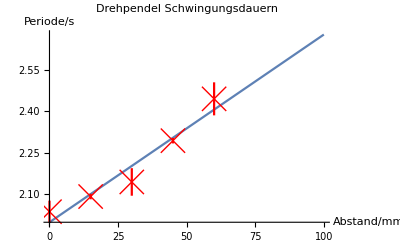

```mathematica
Show[%203,AxesLabel->{HoldForm[Abstand/mm],HoldForm[Periode/s]},PlotLabel->HoldForm[Drehpendel Schwingungsdauern],LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Rasterize[%203,"Image"]
```

-Graphics-

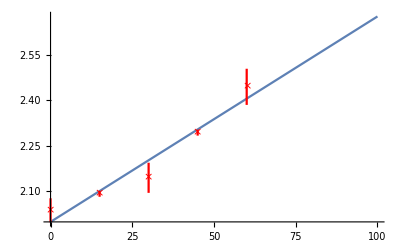

```mathematica
Show[%194,ImageSize->Full]
```

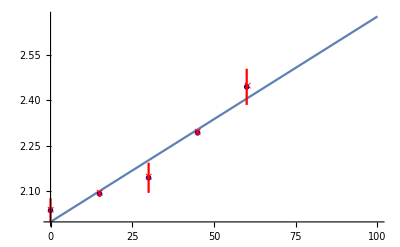

```mathematica
Show[%192,ImageSize->Full]
```

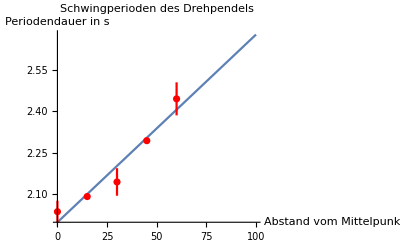

```mathematica
Show[%159,ImageSize->Full]
```

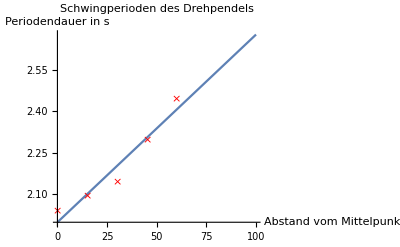

```mathematica
Show[%154,ImageSize->Full]
```

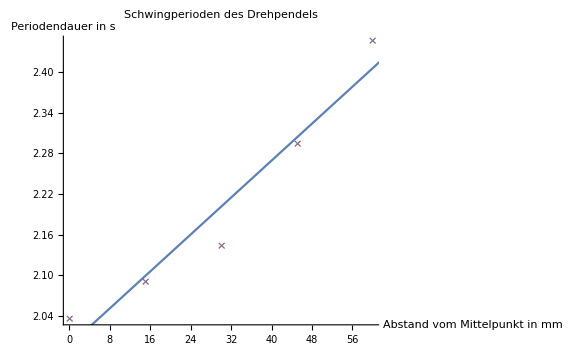

```mathematica
Show[%144,ImageSize->Large]
```

```mathematica
Show[%145,Background->White]
```

-Graphics-

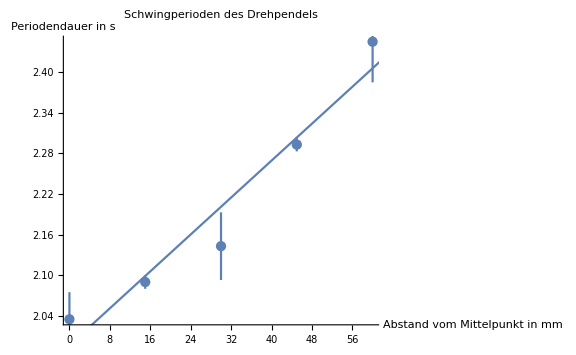

```mathematica
Show[%141,ImageSize->Large]
```

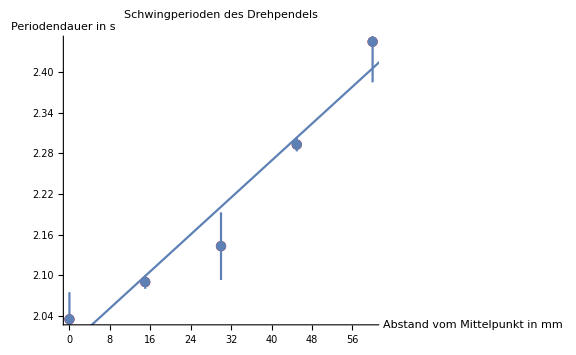

```mathematica
Show[%136,ImageSize->Large]
```

```mathematica
Show[%137,Background->White]
```

-Graphics-